```mathematica
alpha:=1/137;Mz:=92;thetaw:=0.23120;
F1:=Function[{kaa,kgg,lambda},8*(kgg/kaa)^2*alpha/12*Mz^5*thetaw*kaa^2*1/lambda^2][-0.254,0.217,x];F2:=Function[{kaa,kgg,lambda},8*(kgg/kaa)^2*alpha/12*Mz^5*thetaw*kaa^2*1/lambda^2][-0.333,0.054,x];F3:=Function[{kaa,kgg,lambda},8*(kgg/kaa)^2*alpha/12*Mz^5*thetaw*kaa^2*1/lambda^2][-0.340,-0.108,x];F4:=Function[{kaa,kgg,lambda},8*(kgg/kaa)^2*alpha/12*Mz^5*thetaw*kaa^2*1/lambda^2][0.010,-0.108,x];F5:=Function[{kaa,kgg,lambda},8*(kgg/kaa)^2*alpha/12*Mz^5*thetaw*kaa^2*1/lambda^2][0.095,0.217,x];
```

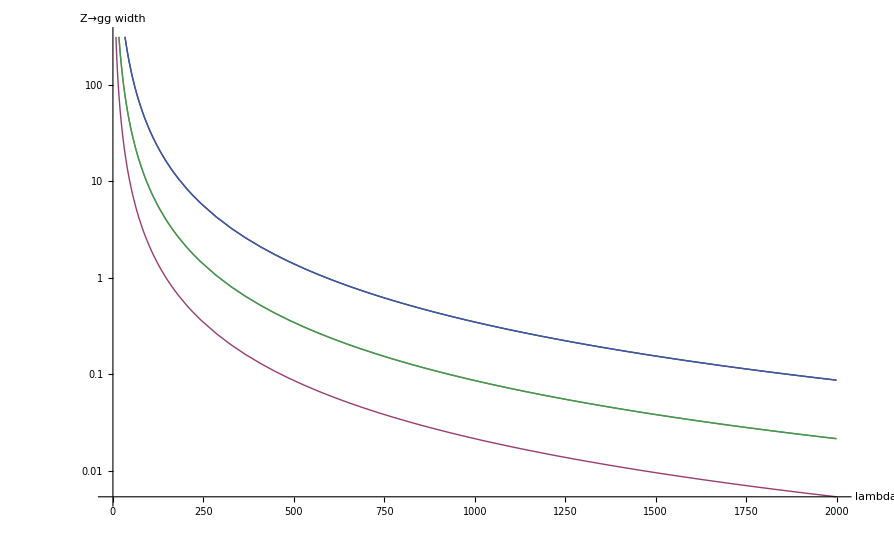

```mathematica
LogPlot[{F1,F2,F3,F4,F5},{x,0,2000},AxesLabel->{"lambda","Z→gg  width"}]
```

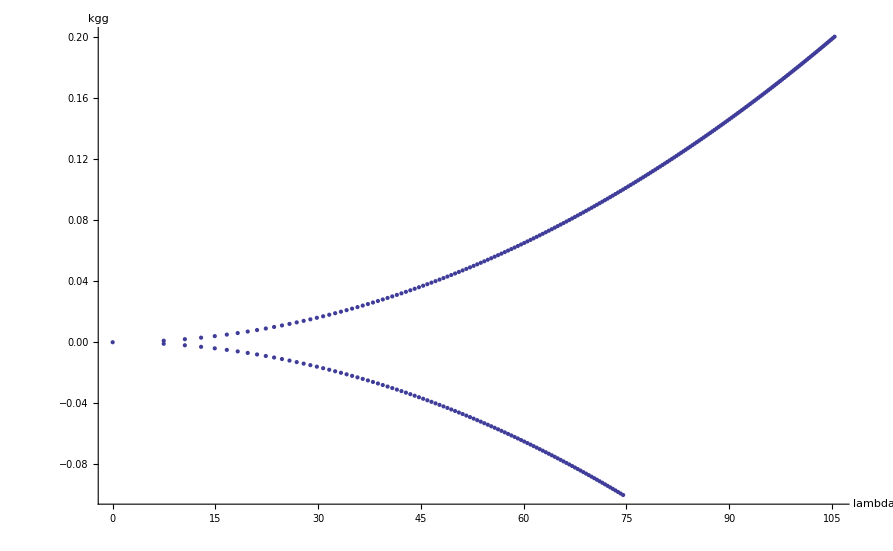

```mathematica
sinwb2:=0.23120;mz:=91.1876;alpha:=1/137;width:=0.0023;
lambda:=Function[{kgg},(8/12*(kgg^2)*alpha*(mz^5)*sinwb2*1/width)^(1/4)][kgg];
ListPlot[Table[{lambda,kgg},{kgg,-0.1,0.2,0.001}],AxesLabel->{"lambda","kgg"}]
```